|r-1/r|/(r+1/r)=a, r>0, a>0

WolframAlphaQueryResults

```mathematica
r:=Sqrt[(1-1/2)/(1+1/2)]
```

```mathematica
d:=(r+1/r)
```

```mathematica
w[t_]:=(-2*I/d)*(r*Exp[I*t]+(1/r)*Exp[-I*t])
```

```mathematica
w[t]
```

-(2 ⅈ (√3 ⅇ^(-ⅈ t)+ⅇ^(ⅈ t)/(√3)))/(1/(√3)+√3)

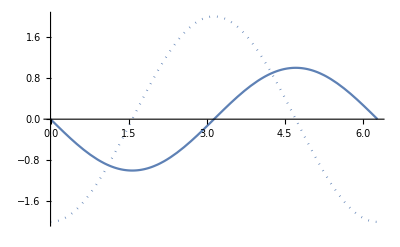

```mathematica
ReImPlot[w[t], {t,0,2*Pi}]
```

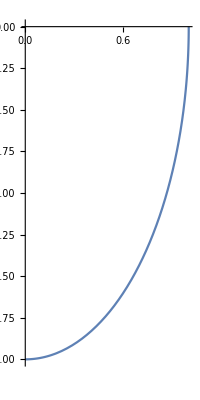

```mathematica
ParametricPlot[ReIm[w[t]], {t,0,-Pi/2}]
```

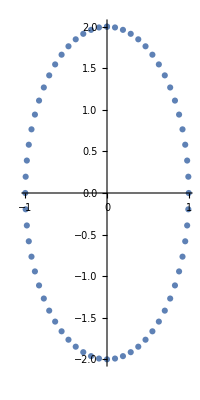

```mathematica
data=Table[w[t],{t,0,2*Pi,2*Pi/64}];
ComplexListPlot[data]
```